```mathematica
GraphConvexHull[graph_?UndirectedGraphQ,vertexSet_]/;SimpleGraphQ[graph]:=Block[{nodes,subset},nodes=VertexList[graph];subset=Subsets[vertexSet,{2}];FindShortestPath[graph,First[#],Last[#]]&/@subset]
```

```mathematica
Subsets[{1,2,9},{2}]
```

{{1,2},{1,9},{2,9}}

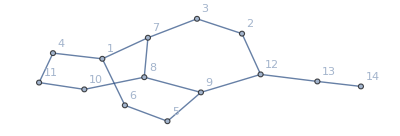

```mathematica
example=Graph[{1<->4,4<->11,11<->10,10<->8,8<->7,7<->1,8<->9,7<->3,2<->3,2<->12,12<->13,13<->14,12<->9,9<->5,5<->6,6<->1},VertexLabels->Automatic]
```

```mathematica
GraphConvexHull[example,{1,2,9}]
```

{{1,7,3,2},{1,7,8,9},{2,12,9}}

```mathematica
f[First[#],Last[#]]&/@Subsets[{1,2,9},{2}]
```

{f[1,2],f[1,9],f[2,9]}

```mathematica
FindShortestPath[example,First[#],Last[#]]&/@Subsets[{1,2,9},{2}]
```

{{1,7,3,2},{1,7,8,9},{2,12,9}}

```mathematica
GraphConvexHull[example,#]&/@GraphConvexHull[example,{1,2,9}]
```

{{{1,7},{1,7,3},{1,7,3,2},{7,3},{7,3,2},{3,2}},{{1,7},{1,7,8},{1,7,8,9},{7,8},{7,8,9},{8,9}},{{2,12},{2,12,9},{12,9}}}

```mathematica
ContainsAll[Flatten[GraphConvexHull[example,#]&/@GraphConvexHull[example,{1,2,9}]],VertexList[example]]
```

False

```mathematica
(Union[Flatten[(GraphConvexHull[example,#]&/@GraphConvexHull[example,{1,2,9}])]])
```

{1,2,3,7,8,9,12}

```mathematica
GraphConvexHull[example,(Union[Flatten[(GraphConvexHull[example,#]&/@GraphConvexHull[example,{1,2,9}])]])]
```

{{1,7,3,2},{1,7,3},{1,7},{1,7,8},{1,7,8,9},{1,7,8,9,12},{2,3},{2,3,7},{2,3,7,8},{2,12,9},{2,12},{3,7},{3,7,8},{3,7,8,9},{3,2,12},{7,8},{7,8,9},{7,8,9,12},{8,9},{8,9,12},{9,12}}

```mathematica
Union[Flatten[GraphConvexHull[example,(Union[Flatten[(GraphConvexHull[example,#]&/@GraphConvexHull[example,{1,2,9}])]])]]]
```

{1,2,3,7,8,9,12}

```mathematica
Union[Flatten[GraphConvexHull[example,(Union[Flatten[(GraphConvexHull[example,#]&/@GraphConvexHull[example,{1,2,9}])]])]]]==(Union[Flatten[(GraphConvexHull[example,#]&/@GraphConvexHull[example,{1,2,9}])]])
```

True

```mathematica
{GraphConvexHull[example,{1,2,9}]}
```

{{{1,7,3,2},{1,7,8,9},{2,12,9}}}

```mathematica
GraphConvexHull[example,{1,2,9}]
```

{{1,7,3,2},{1,7,8,9},{2,12,9}}

```mathematica
Union@@GraphConvexHull[example,{1,2,9}]
```

{1,2,3,7,8,9,12}

```mathematica
GraphConvexHull[example,Union@@GraphConvexHull[example,{1,2,9}]]
```

{{1,7,3,2},{1,7,3},{1,7},{1,7,8},{1,7,8,9},{1,7,8,9,12},{2,3},{2,3,7},{2,3,7,8},{2,12,9},{2,12},{3,7},{3,7,8},{3,7,8,9},{3,2,12},{7,8},{7,8,9},{7,8,9,12},{8,9},{8,9,12},{9,12}}

```mathematica
NestList[Union@@GraphConvexHull[example,#]&,{1,2,9},3]
```

{{1,2,9},{1,2,3,7,8,9,12},{1,2,3,7,8,9,12},{1,2,3,7,8,9,12}}

```mathematica
Most@FixedPointList[Union@@GraphConvexHull[example,#]&,{1,2,9}]
```

{{1,2,9},{1,2,3,7,8,9,12}}

```mathematica
GraphConvexHull[graph_?UndirectedGraphQ,vertexSet_]/;SimpleGraphQ[graph]:=Block[{nodes,subset},nodes=VertexList[graph];subset=Subsets[vertexSet,{2}];FindShortestPath[graph,First[#],Last[#]]&/@subset]
```

```mathematica
Function[{graph,vertexSet},FindShortestPath[graph,First[#],Last[#]]&/@Subsets[vertexSet,{2}]][example,{1,2,9}]
```

{{1,7,3,2},{1,7,8,9},{2,12,9}}

```mathematica
Most@FixedPointList[Union@@Function[{graph,vertexSet},FindShortestPath[graph,First[#],Last[#]]&/@Subsets[vertexSet,{2}]][example,#]&,{1,2,9}]
```

{{1,2,9},{1,2,3,7,8,9,12}}

```mathematica
ClearAll[GraphConvexHull]
```

```mathematica
GraphConvexHull[graph_?GraphQ,vertexSet_]:=Union@@Most@FixedPointList[Union@@Function[{g,v},FindPath[g,First[#],Last[#],GraphDistance[g,First[#],Last[#]],All]&/@Subsets[v,{2}]][graph,#]&,vertexSet]
```

```mathematica
GraphConvexHull[example,{1,2,9}]
```

GraphDistance::inv: The argument {2,12,9} in GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 6, 5, 9}] is not a valid vertex.

FindPath::inv: The argument {2,12,9} in FindPath[Graph[<14>, <16>], {2, 12, 9}, {1, 6, 5, 9}, GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 6, 5, 9}], All] is not a valid vertex.

GraphDistance::inv: The argument {2,12,9} in GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 3, 2}] is not a valid vertex.

FindPath::inv: The argument {2,12,9} in FindPath[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 3, 2}, GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 3, 2}], All] is not a valid vertex.

GraphDistance::inv: The argument {2,12,9} in GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 8, 9}] is not a valid vertex.

FindPath::inv: The argument {2,12,9} in FindPath[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 8, 9}, GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 8, 9}], All] is not a valid vertex.

GraphDistance::inv: The argument {1,6,5,9} in GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 3, 2}] is not a valid vertex.

FindPath::inv: The argument {1,6,5,9} in FindPath[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 3, 2}, GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 3, 2}], All] is not a valid vertex.

GraphDistance::inv: The argument {1,6,5,9} in GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 8, 9}] is not a valid vertex.

FindPath::inv: The argument {1,6,5,9} in FindPath[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 8, 9}, GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 8, 9}], All] is not a valid vertex.

GraphDistance::inv: The argument {1,7,3,2} in GraphDistance[Graph[<14>, <16>], {1, 7, 3, 2}, {1, 7, 8, 9}] is not a valid vertex.

FindPath::inv: The argument {1,7,3,2} in FindPath[Graph[<14>, <16>], {1, 7, 3, 2}, {1, 7, 8, 9}, GraphDistance[Graph[<14>, <16>], {1, 7, 3, 2}, {1, 7, 8, 9}], All] is not a valid vertex.

FindPath::argb: FindPath called with 12 arguments; between 3 and 5 arguments are expected.

FindPath::argb: FindPath called with 2 arguments; between 3 and 5 arguments are expected.

GraphDistance::inv: The argument … in GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], All] is not a valid vertex.

FindPath::inv: The argument … in FindPath[Graph[<14>, <16>], Graph[<14>, <16>], All, GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], All], All] is not a valid vertex.

GraphDistance::inv: The argument … in GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 6, 5, 9}]] is not a valid vertex.

FindPath::inv: The argument … in FindPath[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 6, 5, 9}], GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 6, 5, 9}]], All] is not a valid vertex.

GraphDistance::inv: The argument … in GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 3, 2}]] is not a valid vertex.

FindPath::inv: The argument … in FindPath[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 3, 2}], GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 3, 2}]], All] is not a valid vertex.

GraphDistance::inv: The argument … in GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 8, 9}]] is not a valid vertex.

FindPath::inv: The argument … in FindPath[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 8, 9}], GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {2, 12, 9}, {1, 7, 8, 9}]], All] is not a valid vertex.

GraphDistance::inv: The argument … in GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 3, 2}]] is not a valid vertex.

FindPath::inv: The argument … in FindPath[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 3, 2}], GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 3, 2}]], All] is not a valid vertex.

GraphDistance::inv: The argument … in GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 8, 9}]] is not a valid vertex.

FindPath::inv: The argument … in FindPath[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 8, 9}], GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 6, 5, 9}, {1, 7, 8, 9}]], All] is not a valid vertex.

GraphDistance::inv: The argument … in GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 7, 3, 2}, {1, 7, 8, 9}]] is not a valid vertex.

FindPath::inv: The argument … in FindPath[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 7, 3, 2}, {1, 7, 8, 9}], GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], GraphDistance[Graph[<14>, <16>], {1, 7, 3, 2}, {1, 7, 8, 9}]], All] is not a valid vertex.

GraphDistance::inv: The argument … in GraphDistance[Graph[<14>, <16>], Graph[<14>, <16>], {2, 12, 9}] is not a valid vertex.

```mathematica
Union@@GraphConvexHull[example,{1,2,9}]
```

{1,2,3,7,8,9,12}

```mathematica
FindShortestPath[example,1,9]
```

{1,7,8,9}

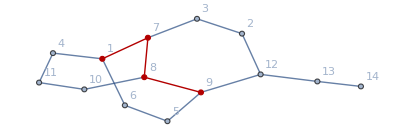

```mathematica
HighlightGraph[Graph[{1, 4, 11, 10, 8, 7, 9, 3, 2, 12, 13, 14, 5, 6}, , {VertexLabels -> {Automatic}}],PathGraph[{1,7,8,9}]]
```

```mathematica
Unprotect["FindShortestPath"]
```

{FindShortestPath}

```mathematica
PersistResourceFunction["PrintDefinitions"]
```

Success[…]

```mathematica
PrintDefinitions["FindShortestPath"]
```

```mathematica
FindShortestPath[example,1,9]
```

{1,7,8,9}

```mathematica
FindPath[example,1,9,GraphDistance[example,1,9],All]
```

{{1,6,5,9},{1,7,8,9}}

```mathematica
Function[in,Union@Flatten@Function[{g,v},FindPath[g,First[#],Last[#],GraphDistance[g,First[#],Last[#]],All]&/@Subsets[v,{2}]][example,in]][{1,2,9}]
```

{1,2,3,5,6,7,8,9,12}

```mathematica
FixedPointList[Function[in,Union@Flatten@Function[{g,v},FindPath[g,First[#],Last[#],GraphDistance[g,First[#],Last[#]],All]&/@Subsets[v,{2}]][example,in]][#]&,{1,2,9}]
```

{{1,2,9},{1,2,3,5,6,7,8,9,12},{1,2,3,5,6,7,8,9,12}}

```mathematica
FixedPoint[Function[in,Union@Flatten@Function[{g,v},FindPath[g,First[#],Last[#],GraphDistance[g,First[#],Last[#]],All]&/@Subsets[v,{2}]][example,in]][#]&,{1,2,9}]
```

{1,2,3,5,6,7,8,9,12}

```mathematica
?GraphConvexHull
```

Missing[UnknownSymbol,GraphConvexHull]

```mathematica
GraphConvexHull[graph_?GraphQ,vertexSet_]:=FixedPoint[Function[in,Union@Flatten@Function[{g,v},FindPath[g,First[#],Last[#],GraphDistance[g,First[#],Last[#]],All]&/@Subsets[v,{2}]][example,in]][#]&,{1,2,9}]/;SubsetQ[VertexList[graph],vertexSet]
```

```mathematica
GraphConvexHull[example,{1,2,9}]
```

{1,2,3,5,6,7,8,9,12}

```mathematica
?GraphConvexHull
```